## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="TPI";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_TPI_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/TPI/

## Import Data

```mathematica
Get["MASSef`"];
```

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{{{g3p,Null}},Keq substrate}

{9.35,Keq value}

{g3p,Km or S05 substrate}

{0.00103,Km or S05 value}

{{{g3p,Null}},kcat substrates}

{9000,kcat value}

{2-phosphoglycolate,Inhibition or activation constant substrate}

{0.006,Inhibition or activation constant value}

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Ki | 2-phosphoglycolate | 0.006 | 0.0057
0.0063 |  | Competitive | dhap | Null | M | 7.6 | 25 | teoahcl | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1}(*{10}*);
s05Priorities = Null;
kcatPriorities = {1}(*{0.0001}*);
inhibitionPriorities={0};
activationPriorities = Null;
otherParamsPriorities =Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c⇌dhap^c)^TPI

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 9.35 | 8.8825
9.8175 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | 0.00103 | 0.00093
0.00113 |  | M | 7.6 | 25 | teoahcl | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null | 27025.3 | 26523.8
27526.8 | 1/s | 7.6 | 37 | teoahcl | 0.1 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### mechanism

```mathematica
catalyticBranch={"E_TPI[c] + g3p[c] <=> E_TPI[c]&g3p",
				"E_TPI[c]&g3p <=> E_TPI[c]&dhap",
				"E_TPI[c]&dhap <=> E_TPI[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((TPI^c)_^+g3p^c⇌(TPI^c&g3p^c)_^)^TPI1,((TPI^c&dhap^c)_^⇌(TPI^c)_^+dhap^c)^TPI2,((TPI^c&g3p^c)_^⇌(TPI^c&dhap^c)_^)^TPI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((TPI^c&g3p^c)_^-((TPI^c&dhap^c)_^)/K_TPI3) Volume_c k_TPI3^⟶}

Volume_c (-(TPI^c&dhap^c)_^ k_TPI3^⟵+(TPI^c&g3p^c)_^ k_TPI3^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.9090909090909091
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	27025.299764582207

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.112353152373473
1	0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.09090909090909086
1	0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.13680688860320997
1	0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.20076000891310164
1	0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.28474724895080133
1	0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.38686317984685675
1	0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.49999999999999983
1	0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.6131368201531431
1	0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7152527510491986
1	0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7992399910868982
1	0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.909090909090909
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	28368.244627081465

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[5]]]
```

Priority	dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/haldaneRatio_1.txt"	9.35
1	0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.09090909090909087
1	0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.20076000891310164
1	0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.28474724895080133
1	0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.3868631798468567
1	0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.4999999999999999
1	0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7152527510491986
1	0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.7992399910868982
1	0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/relRateFor_g3p.txt"	0.9090909090909091
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.
1	0	1	1	7.6	37	"/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI_test/input/absRateFor.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 1.0258510898
best_fit: 1.05728020661
best_fit: 0.299929650563
best_fit: 0.711045710882
best_fit: 1.09213121263
best_fit: 0.611654146906
best_fit: 0.405112664202
best_fit: 1.06095026706
best_fit: 1.08708503632
best_fit: 1.07060322048

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | haldaneRatio_1 | 2.60252×10^-9 | 6.77309×10^-18 | 5.603×10^-8 | 5.99252×10^-7 | 9.35 | 9.35
1 | relRateFor_g3p | 0.000165984 | 2.75506×10^-8 | 0.0000347381 | 0.0382119 | 0.0909091 | 0.0908744
1 | relRateFor_g3p | 0.000135017 | 1.82295×10^-8 | 0.0000425249 | 0.0310839 | 0.136807 | 0.136764
1 | relRateFor_g3p | 0.0000918641 | 8.43901×10^-9 | 0.0000424612 | 0.0211503 | 0.20076 | 0.200718
1 | relRateFor_g3p | 0.0000351868 | 1.23811×10^-9 | 0.0000230695 | 0.00810174 | 0.284747 | 0.284724
1 | relRateFor_g3p | 0.0000337342 | 1.13799×10^-9 | 0.0000300511 | 0.00776788 | 0.386863 | 0.386893
1 | relRateFor_g3p | 0.000110106 | 1.21234×10^-8 | 0.000126781 | 0.0253561 | 0.5 | 0.500127
1 | relRateFor_g3p | 0.000186492 | 3.47792×10^-8 | 0.000263346 | 0.0429506 | 0.613137 | 0.6134
1 | relRateFor_g3p | 0.000255448 | 6.52537×10^-8 | 0.000420829 | 0.0588364 | 0.715253 | 0.715674
1 | relRateFor_g3p | 0.000312171 | 9.74505×10^-8 | 0.0005747 | 0.0719058 | 0.79924 | 0.799815
1 | relRateFor_g3p | 0.000355368 | 1.26286×10^-7 | 0.000706609 | 0.0818599 | 0.863193 | 0.8639
1 | relRateFor_g3p | 0.000386372 | 1.49283×10^-7 | 0.000809137 | 0.089005 | 0.909091 | 0.9099
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3
1 | absRateFor | 5.90012×10^-9 | 3.48114×10^-17 | 0.000367153 | 1.35855×10^-6 | 27025.3 | 27025.3

### Simulated Data and Best Fit Data Plot

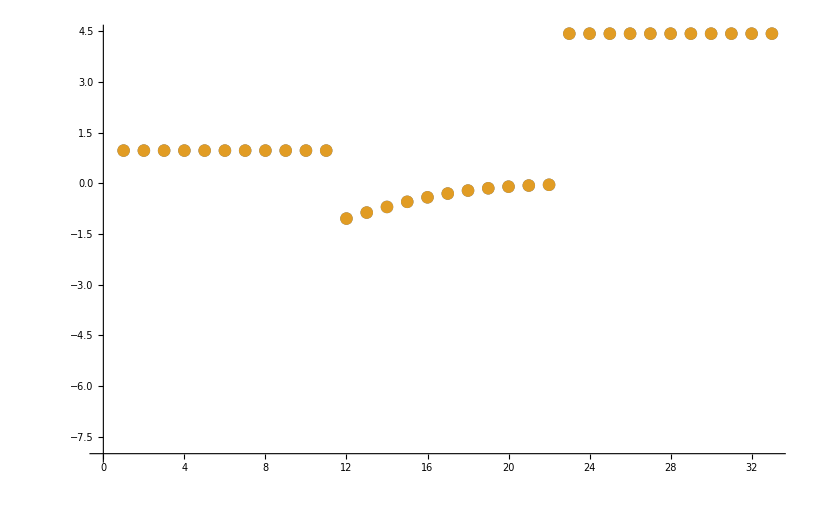

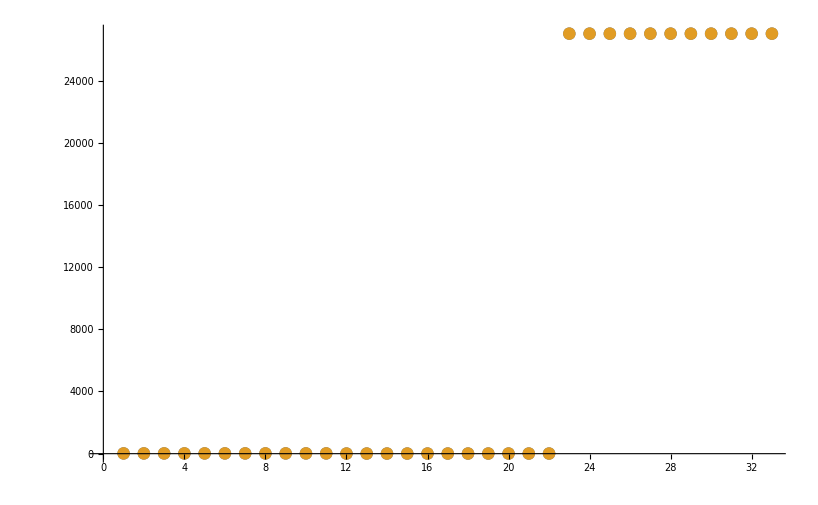

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

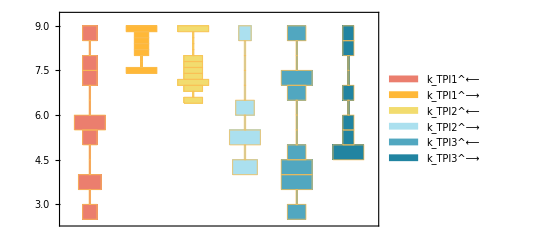

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

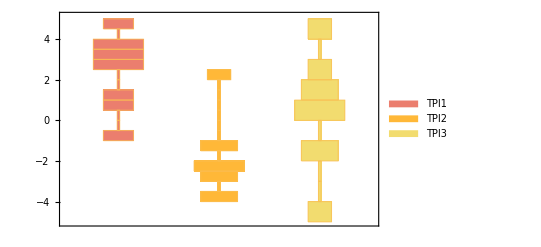

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

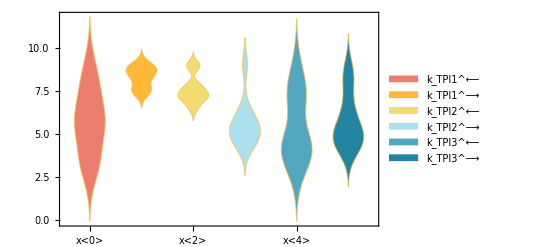

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

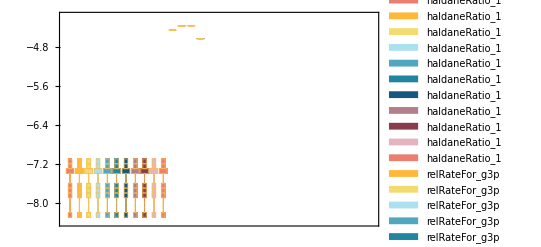

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[1,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00103 | 0.00102948 | 0.0506472

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
27025.3 | 27025.3 | 1.35855×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[1]][[3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
9.35 | 9.35 | 5.99252×10^-7

#### Export rate back calculated parameter error distribution

1

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

4

5

6

7

8

9

10

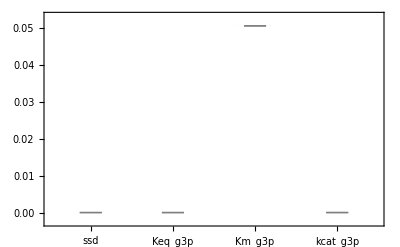

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```